```mathematica
(*Coisinhas iniciais: Potência: ctrl+6, raíz: ctrl+2, fração: ctrl+4, para rodar um módulo (essas barrinhas do lado direito) é só apertar shift+enter*)

(*Plotagem de um gráfico manipulável (Como no desmos)*)

Manipulate[Plot[a*Sin[ω*t+ϕ], {t,-2π,2π}], {a, 1, 10, 1}, {ω, 2π, 20π, π}, {ϕ, 0, 20π,π}]
```

```mathematica
(*Expansão de potências de funções trigonométricas*)

Manipulate[TrigReduce[a*Sin[x]^n+b*Cos[x]^m],{n,0,10,1}, {m,0,10,1}, {a,0, 10,1}, {b,0,10,1}]
```

```mathematica
(* Teste da solução da questão 2 da lista 1 - Expansão de f(x) = cos(αx)*)
α = 1

f[x] = Cos[α*x]
```

1

Cos[x]

```mathematica
Manipulate[Plot[Cos[α x], {x,-5π,5π}], {α, 1, 10, 1}]
```

π

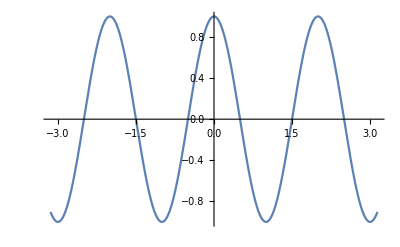

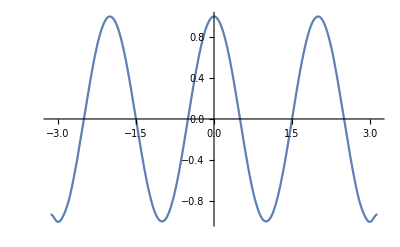

```mathematica
α = π

(*Plotagem teste do excs 2 da lista 1*)
Plot[Cos[α x], {x,-π,π}]
Plot[Sin[α π]/(α π)+ Sum[(-1)^n/π*(2 α)/(α^2-n^2)*Sin[α π]*Cos[n x], {n, 1, 30}], {x, -π,π}]
```

π

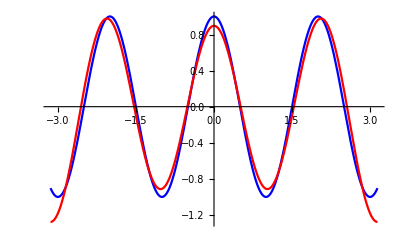

```mathematica
α = 1.1
Plot[{Cos[α x], Sin[α π]/(α π)+ Sum[(-1)^n/π*(2 α)/(α^2-n^2)*Sin[α π]*Cos[n x], {n, 1, 3}]}, {x, -π,π}, PlotStyle->{Blue,Red}]
```

```mathematica
Manipulate[Plot[{Cos[α x], Sin[α π]/(α π)+ Sum[(-1)^n/π*(2 α)/(α^2-n^2)*Sin[α π]*Cos[n x], {n, 1, a}]}, {x, -2π,2π}, PlotStyle->{Blue,Red}], {α,1.1,10π,0.01},{a,1,100,1}]
```

```mathematica
Manipulate[Plot[{x^2, π^2/3+Sum[(4 (-1)^n)/n^2 Cos[n x], {n, 1,a}]}, {x, -2π,2π}, PlotStyle->{Blue,Red}], {a,1,100,2}]
```

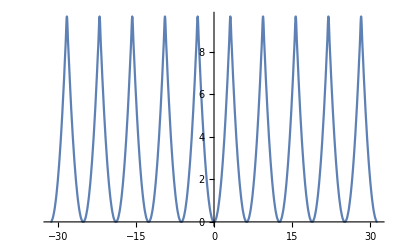

```mathematica
Plot[π^2/3+Sum[(4 (-1)^n)/n^2 Cos[n x], {n, 1,20}], {x, -10π,10π}]
```

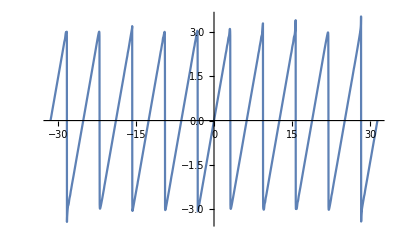

```mathematica
(*Testes sobre funções definidas periódicamente (piecewise periodic)*)
Manipulate[Plot[{x,Sum[(2(-1)^(n+1))/n Sin[n x], {n, 1,a}]}, {x, -2π,2π}, PlotStyle->{Blue,Red}], {a,1,3000,2}]
Plot[Sum[(2(-1)^(n+1))/n Sin[n x], {n, 1,300}], {x, -10π,10π}]
```

2.42

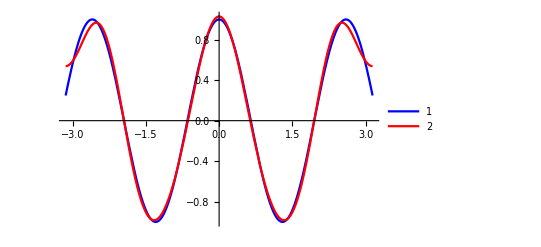

```mathematica
α=2.42
Plot[{Cos[α x], Sin[α π]/(α π)+ Sum[(-1)^n/π*(2 α)/(α^2-n^2)*Sin[α π]*Cos[n x], {n, 1, 5}]}, {x, -π,π}, PlotStyle->{Blue,Red}, PlotLegends->Automatic]
```

```mathematica
(*fourier series of f(x) = e^λx*)
```

0.5

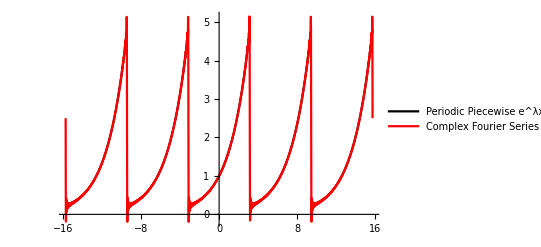

```mathematica
(*Plot da questão 4 da lista 1*)
λ = 0.5
Plot[{E^(λ Mod[x,2π,-π]),Sum[1/(2 π)((-1)^n/(λ - I n))* (E^(λ π) - E^(-λ π))* E^(I n x), {n,-100,100,1}]}, {x,-5π,5π}, PlotStyle->{Black,Red}, PlotLegends->{Piecewise Periodic e^λx, Complex Fourier Series}]
```

```mathematica
(*Nem lembro o que eu estava testando aqui*)
FourierCoefficient[Sin[x],X,n]
```

DiscreteDelta[n] Sin[x]

```mathematica
FourierSinCoefficient[Sin[x]^2,x,n]
```

```mathematica
(4 (-1+Cos[n π]))/((-4 n+n^3) π)
```

(4 (-1+Cos[n π]))/((-4 n+n^3) π)

```mathematica
FourierSeries[E^(E^(-I x)),x,1]
```

1+ⅇ^(-ⅈ x)

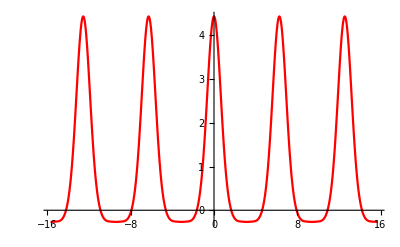

```mathematica
Plot[{E^(E^(-I x)),Sum[E^(-I n x)/Factorial[Abs[n]], {n, -5, 5}]}, {x,-5π,5π}, PlotStyle->{Blue,Red}]
```

```mathematica
Plot[E^(E^(-I x)), {x,1,5}]
```

-Graphics-

```mathematica
(*Plots da questão 8 (feitos de vários jeitos)*)
v = 1;
u = -0;
Plot[{(v - u)/(2π)+Sum[(Sin[k v] - Sin [k u])/(k π)*Cos[k x]+(Cos[k u] - Cos[k v])/(k π)*Sin[k x],{k,1,50}],(v- u)/(2π)+Sum[{(E^(-I a u) - E^(-I a v))/(2π I a)*E^(I a x) },{a,1,50,1}]+Sum[{(E^(-I n u) - E^(-I n v))/(2π I n)*E^(I n x) },{n,-50,-1,1}]},{x,-2π,2π}, PlotRange->Full, PlotStyle->{Blue, Red}, PlotLegends->{Fourier Real, Fourier Complexo}]
```

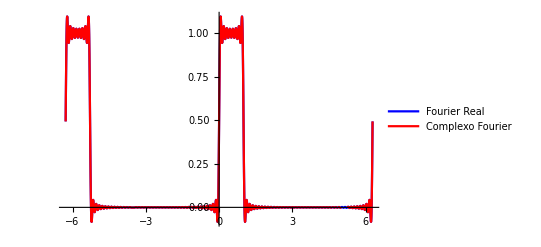
```mathematica
-Graphics-

(*Definição de função por partes! Vc usa isso p fazer a boxcar, por exemplo*)
v = 0.5;
u = -0.5;
F[x_]:=Piecewise[{{1, u<x<v},{0, x<u},{0.5, x=u},{0.5, x=v}}]
Plot[{F[Mod[x,2π,-0.5]],(v - u)/(2π)+Sum[(Sin[k v] - Sin [k u])/(k π)*Cos[k x]+(Cos[k u] - Cos[k v])/(k π)*Sin[k x],{k,1,100}]},{x,-4π,4π}, PlotRange->Full, PlotStyle->{Black, Red}, PlotLegends->{Boxcar, Fourier}]
```

-Graphics-

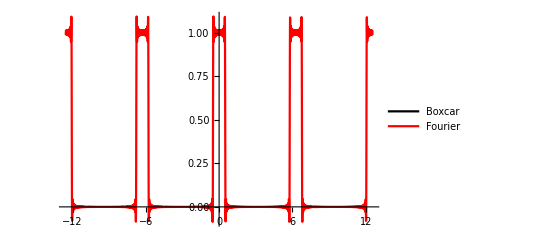

```mathematica
(* Esse plot deu errado e eu n lembro bem o q ela era ieudfnfcjvdikfvnjefv sorry*)
v = 10;
ω = 5;
α = 4;
Manipulate[Plot[{Sum[{(v ⅈ)/(1π n) (-1 + (-1)^n)*ⅇ^(ⅈ n ω x) },{n,1,a,1}]+Sum[{(v ⅈ)/(1π n) (-1 + (-1)^n)*ⅇ^(ⅈ n ω x)},{n,-a,-1,1}]},{x,-2π,2π}], {a,1,10,1}]
Manipulate[Plot[{Sum[{(ⅈ ((-1)^n-1)ω)/(π (ⅈ ω n^2 - α n)) (ⅇ^(x ⅈ n)-ⅇ^((α/ω) x))},{n,1,a,1}]+Sum[{(ⅈ ((-1)^n-1)ω)/(π (ⅈ ω n^2 - α n)) (ⅇ^(x ⅈ n)-ⅇ^((α/ω) x))},{n,-a,-1,1}]},{x,-100,100}, PlotRange->Automatic], {a,1,10,1}]
```

50

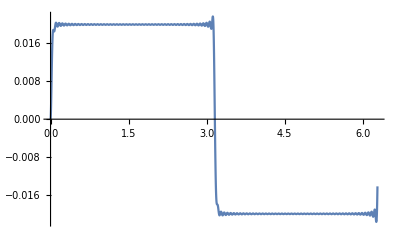

```mathematica
α = 50
Plot[Sum[(2*(E^(I n x)-E^(-x α)))/(π*(I n α - n^2)), {n,-101,101,2}], {x,0,2π}]
```